```mathematica
Clear["Global`*"];
```

```mathematica
gaussian[y0_,A_,μ_, σ_, x_] := y0 + A*Exp[(-2(x-μ)^2)/σ^2];
```

```mathematica
text=Import[FileNameJoin[{NotebookDirectory[],"IntensityX=0.txt"}]];
splt=StringSplit[text,"
"];
Export[FileNameJoin[{NotebookDirectory[],"Data.dat"}],splt[[10;;]]];
data=Import[FileNameJoin[{NotebookDirectory[],"Data.dat"}]];
```

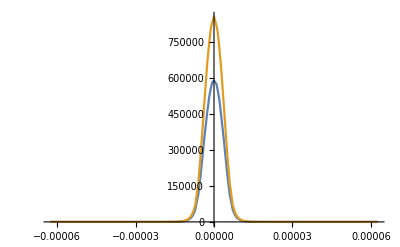

{-Graphics-,-Graphics-}

{MFD1 = 13.6 υm,MFD1 = 13.5 υm}

```mathematica
xColumn=data[[All,1]];
yColumn=data[[All,2]];
E1Column=data[[All,3]];
E2Column=data[[All,4]];
beam1=Sort[Transpose[{yColumn,E1Column}],#1[[1]]<#2[[1]]&];
beam2=Sort[Transpose[{yColumn,E2Column}],#1[[1]]<#2[[1]]&];
ListPlot[Evaluate[{beam1,beam2}],PlotRange->All,Joined->True]
nlm1 = NonlinearModelFit[beam1,gaussian[y0,A,0,σ,x],
{{y0,Min[E1Column]},
{A,Max[E1Column]-Min[E1Column]},
{σ,(Max[yColumn]-Min[yColumn])/2}},
x];
nlm2 = NonlinearModelFit[beam2,gaussian[y0,A,0,σ,x],
{{y0,Min[E1Column]},
{A,Max[E1Column]-Min[E1Column]},
{σ,(Max[yColumn]-Min[yColumn])/2}},
x];
parametersTable1 = nlm1["ParameterTable"];
parametersTable2 = nlm2["ParameterTable"];
y0Fit1=parametersTable1[[1,1,2,2]];
AFit1=parametersTable1[[1,1,3,2]];
μFit1=0;
σFit1=parametersTable1[[1,1,4,2]];
y0Fit2=parametersTable2[[1,1,2,2]];
AFit2=parametersTable2[[1,1,3,2]];
μFit2=0;
σFit2=parametersTable2[[1,1,4,2]];
{Show[
ListPlot[beam1,PlotRange->All,Joined->False,PlotMarkers->{"
StyleBox[\"☺\",\nFontSize->18]"},ImageSize->Medium],
Plot[gaussian[y0Fit1,AFit1,μFit1,σFit1,x],{x,Min[yColumn],Max[yColumn]},ColorFunction->Function[{x,y},Red],PlotRange->All]
],
Show[
ListPlot[beam2,PlotRange->All,Joined->False,PlotMarkers->{"
StyleBox[\"☺\",\nFontSize->18]"},ImageSize->Medium],
Plot[gaussian[y0Fit2,AFit2,μFit2,σFit2,x],{x,Min[yColumn],Max[yColumn]},ColorFunction->Function[{x,y},Red],PlotRange->All]
]}
{"MFD1 = "<>ToString[Round[10×2×Abs[σFit1×10^6]]×0.1]<>" υm","MFD1 = "<>ToString[Round[10×2×Abs[σFit2×10^6]]×0.1]<>" υm"}
```

Должно попасть в диапазон: 13.5 - 14.7

```mathematica
"BeatLength = "<>ToString[Round[10×(1.50×0.001)/(1.4461-1.4458)]×0.1]<>" mm"
```

BeatLength = 5. mm

Должно попасть в диапазон: 1 - 5

Длина биений L=λ/(n_1-n_2)
L(k_1-k_2)=2π
k=(2π n)/λ
L=λ/(n_1-n_2)